```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi}]
```

```mathematica
Fn[teta]:=Cos[(3 π)/2 Cos[teta]]/Sin[teta]
```

```mathematica
Fn[0]
```

Fn[0]

```mathematica
Cos[(3 π)/2 Cos[0.0010]]/Sin[0.0010]
```

-0.00235619

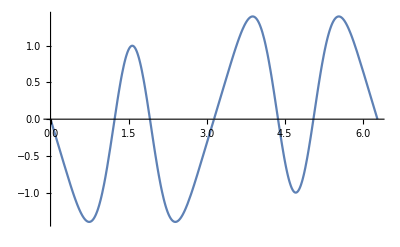

```mathematica
Plot[Cos[(3 π)/2 Cos[teta]]/Sin[teta],{teta,0,2π}]
```

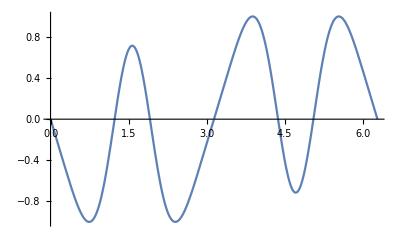

```mathematica
Plot[Cos[(3 π)/2 Cos[teta]]/Sin[teta]*1/1.3990,{teta,0,2π}]
```

Power::infy: Infinite expression 1/0. encountered.

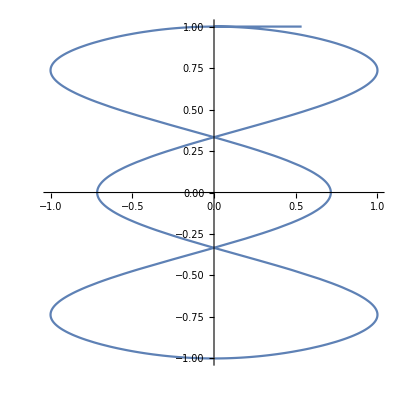

```mathematica
ParametricPlot[{Cos[(3 π)/2 Cos[teta]]/Sin[teta]*1/1.3990,Cos[teta]},{teta,0,2 π}]
```